# Notebook for : Data for the Numerical Calculation of the Kruskal Space-Time by Schmidt (This Notebook Can Be REDONE)

Geoff Cope
University of Utah
March 17, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article (Change this)

```mathematica
Hyperlink["Data for the Numerical Calculation of the Kruskal Space-Time by  Bernd G. Schmidt in BOOK",
"https://link.springer.com/book/10.1007/3-540-45818-2?error=cookies_not_supported&code=7d9e95a7-ec96-483a-9f13-1c5c1e50c79a"]
```

[Data for the Numerical Calculation of the Kruskal Space-Time by  Bernd G. Schmidt in BOOK](https://link.springer.com/book/10.1007/3-540-45818-2?error=cookies_not_supported&code=7d9e95a7-ec96-483a-9f13-1c5c1e50c79a)

```mathematica
(* "Data for the Numerical Calculation of the Kruskal Space-Time" Bernd G. Schmidt *)
(* Taken from page 283 conformal structure of space-time *) 
(* Insert link to text and original paper here *)
(* REWRITE line element to metric as a function of [lineElement_ , differentials_] *)
```

```mathematica
Hyperlink["Colliding Plane Waves by Griffiths - Book","ftp://nozdr.ru/biblio/kolxoz/P/PGr/Griffiths%20J.B.%20Colliding%20plane%20waves%20in%20general%20relativity%20(OUP,%201991)(ISBN%200198532091)(254s)_PGr_.pdf"]
```

[Colliding Plane Waves by Griffiths - Book](ftp://nozdr.ru/biblio/kolxoz/P/PGr/Griffiths%20J.B.%20Colliding%20plane%20waves%20in%20general%20relativity%20(OUP,%201991)(ISBN%200198532091)(254s)_PGr_.pdf)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 7 Kb

{Utilities`CleanSlate`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[μ]-> dμ , 
Dt[η]-> dη , 
Dt[ν]-> dν , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[ϱ]-> dϱ , 
Dt[φ] -> dφ ,
Dt[ξ]-> dξ ,  
Dt[Δ]-> dΔ , 
Dt[δ]-> dδ , 
Dt[ω]-> dω , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓋]-> d𝓋 , 
Dt[𝓊]-> d𝓊 ,
Dt[𝓍]-> d𝓍 ,
Dt[𝓎]-> d𝓎,   
Dt[𝓏] -> d𝓏,
Dt[T]-> dT,
Dt[X]-> dX, 
Dt[Y]-> dY,
Dt[Z]-> dZ,
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ
};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[μ]→dμ
Dt[η]→dη
Dt[ν]→dν
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[ϱ]→dϱ
Dt[φ]→dφ
Dt[ξ]→dξ
Dt[Δ]→dΔ
Dt[δ]→dδ
Dt[ω]→dω
Dt[𝓉]→d𝓉
Dt[𝓋]→d𝓋
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[𝓎]→d𝓎
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[U]→dU
Dt[V]→dV
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
a/:Dt[a]=0  ;  
b /: Dt[b] = 0 ;  
M /: Dt[M] = 0 ;  (* For Schwarzschild Mass *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

```mathematica
Clear[q]
q = { t , r, θ , ϕ } 
m/:Dt[m]=0 (* This just declares m = constant so that its differential is zero *)
```

{t,r,θ,ϕ}

0

```mathematica
Clear[dΣReplace]
dΣReplace = 
dΣ-> √(dθ^2 + Sin[θ]^2 dϕ^2)
```

dΣ→√(dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[eq14pt2]
eq14pt2 = 
u== t - r  - 2 m Log[r/(2 m)-1 ]
```

u==-r+t-2 m Log[-1+r/(2 m)]

```mathematica
Clear[eq14pt3]
eq14pt3 = 
Collect[ Dt[ u== t - r  - 2 m Log[r/(2 m)-1 ] ] /. dtReplace  , dr ]
```

du==dt+dr (-1-1/(-1+r/(2 m)))

```mathematica
Clear[dtuReplace]
dtuReplace = 
Collect[Flatten[Solve[eq14pt3 , dt ] ] , du ]
```

{dt→du-(dr r)/(2 m-r)}

```mathematica
Clear[eq14pt4]
eq14pt4 = 
v== t + r  + 2 m Log[r/(2 m)-1 ]
```

v==r+t+2 m Log[-1+r/(2 m)]

```mathematica
Clear[uvTransform]
uvTransform = 
Flatten[Solve[ { eq14pt2 , eq14pt4 } , { u , v } ] ]
```

{u→-r+t-2 m Log[-1+r/(2 m)],v→r+t+2 m Log[-1+r/(2 m)]}

```mathematica
Clear[eq14pt5]
eq14pt5 = 
Collect[ Dt[ v== t + r  + 2 m Log[r/(2 m)-1 ] ] /. dtReplace  , dr ]
```

dv==dt+dr (1+1/(-1+r/(2 m)))

```mathematica
Clear[dtvReplace]
dtvReplace = 
Collect[ Flatten[Solve[eq14pt5 , dt ] ] , dv ]
```

{dt→dv+(dr r)/(2 m-r)}

```mathematica
Clear[g]
g = - ( 1 - (2 m)/r) dt^2 + dr^2/(1- (2 m)/r)+ r^2 dΣ^2
```

dr^2/(1-(2 m)/r)+dt^2 (-1+(2 m)/r)+dΣ^2 r^2

```mathematica
Clear[lineelement]
lineelement =g  //.  dΣReplace // Expand  // Simplify
```

dr^2/(1-(2 m)/r)+dt^2 (-1+(2 m)/r)+dθ^2 r^2+dϕ^2 r^2 Sin[θ]^2

```mathematica
Clear[eq14pt6]
eq14pt6 = 
g /. dtuReplace  // Expand  // Simplify
```

-2 dr du+du^2 (-1+(2 m)/r)+dΣ^2 r^2

```mathematica
Clear[eq14pt7]
eq14pt7 = 
g /. dtvReplace   // Expand // Simplify
```

2 dr dv+dv^2 (-1+(2 m)/r)+dΣ^2 r^2

```mathematica
eq14pt2
eq14pt4
```

u==-r+t-2 m Log[-1+r/(2 m)]

v==r+t+2 m Log[-1+r/(2 m)]

```mathematica
Clear[eq14pt9]
eq14pt9 = 
SubtractSides[ eq14pt4 , eq14pt2 ]
```

-u+v==2 r+4 m Log[-1+r/(2 m)]

```mathematica
Dt[ eq14pt9 ]
```

-Dt[u]+Dt[v]==2 Dt[r]+(2 Dt[r])/(-1+r/(2 m))

```mathematica
Dt[ eq14pt9 ]  /. dtReplace
```

-du+dv==2 dr+(2 dr)/(-1+r/(2 m))

```mathematica
Clear[drReplace]
drReplace = 
Flatten[ Solve[ Dt[ eq14pt9 ]  /. dtReplace  , dr ] ]
```

{dr→((du-dv) (2 m-r))/(2 r)}

```mathematica
Clear[eq14pt8]
eq14pt8 = 
Collect[ ( ( g /. dtuReplace  // Expand  )  //. drReplace ) // Expand  // Simplify  , du dv ]
```

du dv (-1+(2 m)/r)+dΣ^2 r^2

```mathematica
Clear[eq14pt10]
eq14pt10 = {
U== - Exp[-u/(4 m)]  ,
V == Exp[v/(4 m)]
};
eq14pt10 // TableForm
```

U==-ⅇ^(-u/(4 m))
V==ⅇ^(v/(4 m))

```mathematica
Clear[UVreplace]
UVreplace = 
Flatten[Solve[ eq14pt10 , { U , V } ] ]
```

{U→-ⅇ^(-u/(4 m)),V→ⅇ^(v/(4 m))}

```mathematica
Clear[uvUVreplace]
uvUVreplace = 
Flatten[Solve[eq14pt10  , { u , v } ] /. { C[1]-> 0 , C[2]-> 0 } ]
```

{u→-4 m Log[-U],v→4 m Log[V]}

```mathematica
Dt[eq14pt10]
Dt[eq14pt10] /. dtReplace
```

{Dt[U]==(ⅇ^(-u/(4 m)) Dt[u])/(4 m),Dt[V]==(ⅇ^(v/(4 m)) Dt[v])/(4 m)}

{dU==(du ⅇ^(-u/(4 m)))/(4 m),dV==(dv ⅇ^(v/(4 m)))/(4 m)}

```mathematica
Flatten[ Solve[ ( Dt[eq14pt10] /. dtReplace ) , { du , dv } ] ]
```

{du→4 dU ⅇ^(u/(4 m)) m,dv→4 dV ⅇ^(-v/(4 m)) m}

```mathematica
Clear[dudvReplace]
dudvReplace = 
Flatten[ Solve[ ( Dt[eq14pt10] /. dtReplace ) , { du , dv } ] ] /. uvUVreplace
```

{du→-(4 dU m)/U,dv→(4 dV m)/V}

```mathematica
eq14pt8
```

du dv (-1+(2 m)/r)+dΣ^2 r^2

```mathematica
Clear[eq14pt11]
eq14pt11 = 
eq14pt8 /. dudvReplace
```

dΣ^2 r^2-(16 dU dV m^2 (-1+(2 m)/r))/(U V)

```mathematica
eq14pt11 /. UVreplace
```

16 dU dV ⅇ^(u/(4 m)-v/(4 m)) m^2 (-1+(2 m)/r)+dΣ^2 r^2

```mathematica
Clear[eq14pt12]
eq14pt12 = 
U V /. UVreplace  /. uvTransform // Expand // FullSimplify  (* Structure of (1 - x)  Exp[x] *)
```

ⅇ^(r/(2 m)) (1-r/(2 m))

```mathematica
eq14pt12  /. r -> 2 m x
```

ⅇ^x (1-x)

```mathematica
Clear[eq14pt13]
eq14pt13 = 
eq14pt11 /. UVreplace  /. uvTransform // Simplify
```

-(32 dU dV ⅇ^(-r/(2 m)) m^3)/r+dΣ^2 r^2

```mathematica
Flatten[Solve[ y== x Exp[x] , x ]]  (* See eq 14 pt 14 for LambertW  and compare to ProductLog *)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→ProductLog[y]}

```mathematica
?ProductLog
```

```mathematica
eq14pt12  /. r -> 2 m x
```

ⅇ^x (1-x)

```mathematica
Clear[eq14pt14]
eq14pt14 = 
Flatten[ Solve[ y == eq14pt12  /. r -> 2 m x  , x ] ] /. { x -> r/(2 m), y -> U V }
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r/(2 m)→1+ProductLog[-(U V)/ⅇ]}

```mathematica
eq14pt6
```

-2 dr du+du^2 (-1+(2 m)/r)+dΣ^2 r^2

```mathematica
Flatten[Solve[ l== 1/r , r ] ]
```

{r→1/l}

```mathematica
Clear[rdrReplace]
rdrReplace = 
Union[
 Flatten[Solve[ l== 1/r , r ] ] ,
Flatten[Solve[ ( Dt[ l== 1/r ]  /. dtReplace ) , dr ] ]
];
rdrReplace // TableForm
```

dr→-dl r^2
r→1/l

```mathematica
Clear[eq14pt15]
eq14pt15 = 
eq14pt6  //.  rdrReplace (* make sure to use //. so also replaces r^2 *)
```

(2 dl du)/l^2+dΣ^2/l^2+du^2 (-1+2 l m)

```mathematica
Clear[eq14pt16]
eq14pt16 = 
Collect[ l^2 eq14pt15 // Expand  , du^2] // Simplify
```

2 dl du+dΣ^2+du^2 l^2 (-1+2 l m)

```mathematica
Clear[eq14pt17]
eq14pt17  = eq14pt16 - dΣ^2
```

2 dl du+du^2 l^2 (-1+2 l m)

```mathematica
Clear[dlReplace]
dlReplace = 
Flatten[Solve[ eq14pt17 == 0  , dl ] ]
```

{dl→-1/2 du l^2 (-1+2 l m)}

```mathematica
Flatten[Solve[ Collect[ ( eq14pt17 // Expand )  == 0 , du ] , dl ] ]  /. dl-> l'[u] du
```

{du l'[u]→-1/2 du (-l^2+2 l^3 m)}

```mathematica
Clear[eq14pt18]
eq14pt18 = 
Assuming[ du ≠ 0 , 
DivideSides[ du l'[u]==-1/2 du (-l^2+2 l^3 m) , du ] ]
```

l'[u]==1/2 (l^2-2 l^3 m)

```mathematica
Flatten[DSolve[ eq14pt18 /. l'[u]-> 1/u'[l] , u[l] , l ]  /. C[1]-> 0 ]
```

{u[l]→2 (-1/l+2 m Log[l]-2 m Log[1-2 l m])}

```mathematica
eq14pt18[[2]] /. l-> l[u]
```

1/2 (l[u]^2-2 m l[u]^3)

```mathematica
Clear[eq14pt18a]
eq14pt18a = 
eq14pt18[[1]] ==  (  ( eq14pt18[[2]] /. l-> l[u] ) // FullSimplify )
```

l'[u]==1/2 l[u]^2 (1-2 m l[u])

```mathematica
(* Not quite sure what to do here *) 
Assuming[ l[u]≠ 0 && m ≠ 1/(2 l[u])  , 
Flatten[DSolve[ eq14pt18a , l[u] , u ] ]] /. C[1]-> 0
```

{l[u]→InverseFunction[-2 m Log[#1]+2 m Log[1-2 m #1]+1/#1&][-u/2]}

```mathematica
eq14pt18a[[2]]  // Apart
```

l[u]^2/2-m l[u]^3

```mathematica
Clear[eq14pt19] (* use [esc]scv [esc] for 𝓋 instead of v *)  
                                    (* book leaves out 2m in front of second log *) 
eq14pt19 = 
 u == -2 ( 1/l+ 2 m Log[1/l- 2 m ] ) + 2 (1/𝓋+ 2 m Log[1/𝓋-2 m ] )
```

u==-2 (1/l+2 m Log[1/l-2 m])+2 (1/𝓋+2 m Log[-2 m+1/𝓋])

```mathematica
Clear[eq14pt20]
eq14pt20 = 
Collect[ Dt[ eq14pt19 ]  /. dtReplace  , { dl , d𝓋 } ]
```

du==dl (2/l^2+(4 m)/(l^2 (1/l-2 m)))+d𝓋 (-2/𝓋^2-(4 m)/((-2 m+1/𝓋) 𝓋^2))

```mathematica
Clear[dlReplace]
dlReplace  = 
Flatten[Collect[ Solve[ eq14pt20 , dl ]  // Apart  , dl ]  // Simplify ]
```

{dl→(l^2 (-1+2 l m) (2 d𝓋+du 𝓋^2 (1-2 m 𝓋)))/(2 𝓋^2 (-1+2 m 𝓋))}

```mathematica
Clear[eq14pt21]
eq14pt21 = 
eq14pt16 /. dlReplace // Expand // FullSimplify
```

dΣ^2+(2 du d𝓋 l^2 (-1+2 l m))/(𝓋^2 (-1+2 m 𝓋))

```mathematica
eq14pt9 
eq14pt9  /. u-> 0 
rdrReplace[[2]]
eq14pt9  /. u-> 0  /. rdrReplace[[2]]
eq14pt9  /. u-> 0  /. rdrReplace[[2]] /. l-> 𝓋 (* v goes to [esc]scv[esc] for script v ,  𝓋 *)
```

-u+v==2 r+4 m Log[-1+r/(2 m)]

v==2 r+4 m Log[-1+r/(2 m)]

r→1/l

v==2/l+4 m Log[-1+1/(2 l m)]

v==2/𝓋+4 m Log[-1+1/(2 m 𝓋)]

```mathematica
Clear[eq14pt23]
eq14pt23 = 
eq14pt9  /. u-> 0  /. rdrReplace[[2]] /. l-> 𝓋 (* v goes to [esc]scv[esc] for script v ,  𝓋 *)
```

v==2/𝓋+4 m Log[-1+1/(2 m 𝓋)]

```mathematica
Clear[vReplace]
vReplace = 
Flatten[Solve[ eq14pt23 , v ] ] // Expand
```

{v→2/𝓋+4 m Log[-1+1/(2 m 𝓋)]}

```mathematica
eq14pt10
eq14pt10[[2]]
eq14pt10[[2,2]]
eq14pt10[[2,2]] /. vReplace  // PowerExpand  // Apart  (* Book can't be right *)
```

{U==-ⅇ^(-u/(4 m)),V==ⅇ^(v/(4 m))}

V==ⅇ^(v/(4 m))

ⅇ^(v/(4 m))

ⅇ^(1/(2 m 𝓋)) (-1+1/(2 m 𝓋))

```mathematica
Clear[eq14pt23a]
eq14pt23a = 
eq14pt9  /. v-> 0  /. rdrReplace[[2]] /. l-> 𝓊 (* v goes to [esc]scu[esc] for script u ,  𝓋 *)
```

-u==2/𝓊+4 m Log[-1+1/(2 m 𝓊)]

```mathematica
Clear[uReplace]
uReplace = 
Flatten[Solve[eq14pt23a , u]] // Apart
```

{u→-2/𝓊-4 m Log[-1+1/(2 m 𝓊)]}

```mathematica
Clear[duReplace]
duReplace = 
Dt[ uReplace ] /. dtReplace
```

{du→(2 d𝓊)/𝓊^2+(2 d𝓊)/((-1+1/(2 m 𝓊)) 𝓊^2)}

```mathematica
eq14pt10
eq14pt10[[1]]
eq14pt10[[1,2]]
eq14pt10[[1,2]] /. uReplace  // PowerExpand  // Apart  (* Book can't be right *)
```

{U==-ⅇ^(-u/(4 m)),V==ⅇ^(v/(4 m))}

U==-ⅇ^(-u/(4 m))

-ⅇ^(-u/(4 m))

-ⅇ^(1/(2 m 𝓊)) (-1+1/(2 m 𝓊))

```mathematica
Clear[eq14pt24]
eq14pt24 = 
eq14pt10[[2,2]] /. vReplace  // PowerExpand  // Apart  (* Book can't be right *)
```

ⅇ^(1/(2 m 𝓋)) (-1+1/(2 m 𝓋))

```mathematica
Clear[eq14pt25]
eq14pt25 = 
eq14pt9  /. v-> 0  /. rdrReplace[[2]] /. l-> 𝓊 (* v goes to [esc]scu[esc] for script u ,  𝓊 *)
```

-u==2/𝓊+4 m Log[-1+1/(2 m 𝓊)]

```mathematica
Clear[eq14pt26]
eq14pt26 = 
eq14pt10[[1,2]] /. uReplace  // PowerExpand  // Apart  (* Book can't be right *)
```

-ⅇ^(1/(2 m 𝓊)) (-1+1/(2 m 𝓊))

```mathematica
eq14pt25
```

-u==2/𝓊+4 m Log[-1+1/(2 m 𝓊)]

```mathematica
Dt[eq14pt25]
```

-Dt[u]==-(2 Dt[𝓊])/𝓊^2-(2 Dt[𝓊])/((-1+1/(2 m 𝓊)) 𝓊^2)

```mathematica
Dt[eq14pt25]  /. dtReplace
```

-du==-(2 d𝓊)/𝓊^2-(2 d𝓊)/((-1+1/(2 m 𝓊)) 𝓊^2)

```mathematica
Clear[duReplace]
duReplace = 
Flatten[Solve [ Dt[eq14pt25]  /. dtReplace  , du ] ]
```

{du→-(2 d𝓊)/(𝓊^2 (-1+2 m 𝓊))}

```mathematica
eq14pt21
```

dΣ^2+(2 du d𝓋 l^2 (-1+2 l m))/(𝓋^2 (-1+2 m 𝓋))

```mathematica
Clear[eq14pt27]
eq14pt27 = 
eq14pt21 /. duReplace (* looks about right, check by hand *)
```

dΣ^2-(4 d𝓊 d𝓋 l^2 (-1+2 l m))/(𝓊^2 (-1+2 m 𝓊) 𝓋^2 (-1+2 m 𝓋))

```mathematica
eq14pt10
eq14pt10[[1,2]]
eq14pt10[[1,2]] /. uReplace // Apart 
eq14pt10[[1,2]] 
eq14pt10[[2,2]] /. vReplace // Apart 
eq14pt12
eq14pt12 /.  rdrReplace[[2]]
```

{U==-ⅇ^(-u/(4 m)),V==ⅇ^(v/(4 m))}

-ⅇ^(-u/(4 m))

-ⅇ^(1/(2 m 𝓊)) (-1+1/(2 m 𝓊))

-ⅇ^(-u/(4 m))

ⅇ^(1/(2 m 𝓋)) (-1+1/(2 m 𝓋))

ⅇ^(r/(2 m)) (1-r/(2 m))

ⅇ^(1/(2 l m)) (1-1/(2 l m))

```mathematica
Clear[eq14pt28]
eq14pt28 = 
( eq14pt12 /.  rdrReplace[[2]])  == ( eq14pt10[[1,2]] /. uReplace // Apart  ) * ( eq14pt10[[2,2]] /. vReplace // Apart  ) 
(* Off by a factor of 2 in each exponential denominator, figure out why *)
```

ⅇ^(1/(2 l m)) (1-1/(2 l m))==-ⅇ^(1/(2 m 𝓊)+1/(2 m 𝓋)) (-1+1/(2 m 𝓊)) (-1+1/(2 m 𝓋))

```mathematica
Series[ eq14pt28   /. l-> C[1] // Expand  , { 𝓋 , 0 , 1 } , { 𝓊 , 0 , 1 } ]  // Normal
Series[ eq14pt28  /. l-> C[1] // Expand  , { 𝓋 , 0 , 1 } ]   // Normal //Simplify
```

ⅇ^(1/(2 m C[1]))-ⅇ^(1/(2 m C[1]))/(2 m C[1])==ⅇ^(1/(2 m 𝓊)+1/(2 m 𝓋)) (-1+1/(2 m 𝓊)+(1/(2 m)-1/(4 m^2 𝓊))/𝓋)

(ⅇ^((𝓊+𝓋)/(2 m 𝓊 𝓋)) (-1+2 m 𝓊) (-1+2 m 𝓋))/(m 𝓊 𝓋)+(2 ⅇ^(1/(2 m C[1])) (-1+2 m C[1]))/C[1]==0

```mathematica
(* Skipping to section 14 pt 3 *)
```

```mathematica
Clear[eq14pt31]
eq14pt31 = 
𝒽 == dr^2/(1 - 1/r+ (𝓀^2 r^2)/9)+ r^2 dΣ^2 (* use [esc]sch[esc] for 𝒽 and [esc]sck[esc] for 𝓀 *)
```

𝒽==dΣ^2 r^2+dr^2/(1-1/r+(r^2 𝓀^2)/9)

```mathematica
eq14pt31[[2,2]]
Denominator[eq14pt31[[2,2]]]
```

dr^2/(1-1/r+(r^2 𝓀^2)/9)

1-1/r+(r^2 𝓀^2)/9

```mathematica
Denominator[eq14pt31[[2,2]]] /. 𝓀-> 6
```

1-1/r+4 r^2

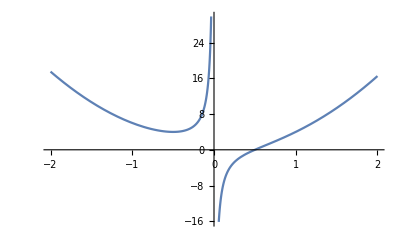

```mathematica
Plot[
Evaluate[
Denominator[( eq14pt31[[2,2]] /. 𝓀-> 6   )]] , { r , -2 , 2 } ]  (* positive for r > 1/2 *)
```

```mathematica
Solve[ Denominator[( eq14pt31[[2,2]] /. 𝓀-> 6   )] == 0 , r ]
```

{{r→1/2},{r→1/4 (-1-ⅈ √7)},{r→1/4 (-1+ⅈ √7)}}

```mathematica
Clear[rlReplace]
rlReplace = Union[ Flatten[Solve[ l== 1/r , r ] ] , Flatten[Solve[ l== 1/r , l ] ]]
```

{l→1/r,r→1/l}

```mathematica
Clear[drtodlReplace]
drtodlReplace = 
Flatten[Solve[ Dt[ l== 1/r ]  /. dtReplace  , dr ]]  /. rlReplace
```

{dr→-dl/l^2}

```mathematica
eq14pt31 /. rlReplace[[2]]
```

𝒽==dΣ^2/l^2+dr^2/(1-l+𝓀^2/(9 l^2))

```mathematica
Clear[eq14pt33]
eq14pt33 = 
eq14pt31 /. rlReplace[[2]] /. drtodlReplace /. 𝓀-> 6
```

𝒽==dl^2/((1+4/l^2-l) l^4)+dΣ^2/l^2

```mathematica
Clear[eq14pt34]
eq14pt34 = 
Assuming[  l^2 ≠ 0 , MultiplySides[ eq14pt33 , l^2]] // Expand
```

l^2 𝒽==dΣ^2+dl^2/((1+4/l^2-l) l^2)

```mathematica
Clear[eq14pt35a]
eq14pt15a = 
 w== 2 √(2-l)
```

w==2 √(2-l)

```mathematica
Clear[lReplace]
lReplace = 
Flatten[Solve[ eq14pt15a , l ] ]
```

{l→1/4 (8-w^2)}

```mathematica
Clear[eq14pt15b]
eq14pt15b = 
Dt[ w== 2 √(2-l) ]  /. dtReplace
```

dw==-dl/(√(2-l))

```mathematica
Clear[eq14pt35c]
eq14pt15c = 
eq14pt15b /. lReplace  // Expand  // Simplify // PowerExpand
```

dw==-(2 dl)/w

```mathematica
Flatten[Solve[ eq14pt15c , dl ] ]
```

{dl→-(dw w)/2}

```mathematica
eq14pt34[[2]]
eq14pt34[[2]] /. lReplace
```

dΣ^2+dl^2/((1+4/l^2-l) l^2)

dΣ^2+(16 dl^2)/((8-w^2)^2 (1+64/((8-w^2)^2)+1/4 (-8+w^2)))

```mathematica
Clear[eq14pt38]
eq14pt38  = 
( eq14pt34[[2]] /. lReplace   //. Flatten[Solve[ eq14pt15c , dl ] ] ) // Expand // FullSimplify
```

dΣ^2+(16 dw^2)/(128-20 w^2+w^4)

```mathematica
1/(2+( 2 - 1/4 w^2) + (2 - 1/4 w^2)^2) // ExpandAll  // Together  
(* our form is equivalent to but looks different form theirs *) 
(* eq14pt38 and eq14pt54 *)
```

16/(128-20 w^2+w^4)

```mathematica
eq14pt31
```

𝒽==dΣ^2 r^2+dr^2/(1-1/r+(r^2 𝓀^2)/9)

```mathematica
rlReplace[[2]]
drtodlReplace
```

r→1/l

{dr→-dl/l^2}

```mathematica
Clear[eq14pt39]
eq14pt39 = 
Expand[Assuming[
l^2≠ 0 ,  MultiplySides[ ( eq14pt31  /. rlReplace[[2]] /. drtodlReplace ) , l^2]]]
```

l^2 𝒽==dΣ^2+dl^2/(l^2 (1-l+𝓀^2/(9 l^2)))

```mathematica
Denominator[ eq14pt39[[2,2]] ]  // Expand
```

l^2-l^3+𝓀^2/9

```mathematica
Clear[eq14pt45]
eq14pt45 = 
r'[t]^2== (1-1/r)^2 ( 1 + (9/(𝓀^2 r^2))(1 - 1/r) ) == Z^2
```

r'[t]^2==(1-1/r)^2 (1+(9 (1-1/r))/(r^2 𝓀^2))==Z^2

```mathematica
eq14pt45[[1;;2]]
```

r'[t]^2==(1-1/r)^2 (1+(9 (1-1/r))/(r^2 𝓀^2))

```mathematica
eq14pt45[[2;;3]]
```

(1-1/r)^2 (1+(9 (1-1/r))/(r^2 𝓀^2))==Z^2

```mathematica
Clear[Zreplace]
Zreplace = 
Solve[ eq14pt45[[2;;3]] , Z ][[2]]
```

{Z→((-1+r) √(-9+9 r+r^3 𝓀^2))/(r^(5/2) 𝓀)}

```mathematica
Zreplace[[1,2]]/( 1-1/r) // Expand // Simplify
```

(√(-9+9 r+r^3 𝓀^2))/(r^(3/2) 𝓀)

```mathematica
Clear[ξtangent]
ξtangent = { 1 , ( Z /. Zreplace  ) }
```

{1,((-1+r) √(-9+9 r+r^3 𝓀^2))/(r^(5/2) 𝓀)}

```mathematica
Clear[ξorthogonal]
ξorthogonal = { ( Z/(1 - 1/r) /. Zreplace ) , 1 - 1/r}
```

{((-1+r) √(-9+9 r+r^3 𝓀^2))/((1-1/r) r^(5/2) 𝓀),1-1/r}

```mathematica
Clear[eq14pt46]
eq14pt46 = 
Collect[(  Ω^2 g /. { Ω -> 1/r}  // Apart )  ,{  dr^2 , dt^2} ]  /. m -> 1/2
```

dΣ^2+dt^2 (1/r^3-1/r^2)+dr^2 (1/(-1+r)-1/r)

```mathematica
coefficients = { Coefficient[ eq14pt46 , dt^2]  , Coefficient[ eq14pt46 , dr^2]  }
```

{1/r^3-1/r^2,1/(-1+r)-1/r}

```mathematica
Sum[ coefficients[[i]] ξorthogonal[[i]] ξtangent[[i]] , { i , 1, 2 } ] // Expand // FullSimplify
```

0

```mathematica
Clear[n]
n = a { Z/(1-1/r), 1 - 1/r}
```

{(a Z)/(1-1/r),a (1-1/r)}

```mathematica
Clear[eq14pt50]
eq14pt50 = 
Sum[ coefficients[[i]] n[[i]] n[[i]] , { i , 1, 2 } ] == - 1
```

a^2 (1-1/r)^2 (1/(-1+r)-1/r)+(a^2 (1/r^3-1/r^2) Z^2)/(1-1/r)^2==-1

```mathematica
Clear[eq14pt51]
eq14pt51 = 
PowerExpand[FullSimplify[Expand[Solve[ ( eq14pt50 // Expand // Simplify  ) , a ]  /. Zreplace ]]][[2]]
```

{a→(r^3 𝓀)/(3 (-1+r))}

```mathematica
n[[2]]
n[[2]] /. eq14pt51  // Expand  // FullSimplify
```

a (1-1/r)

(r^2 𝓀)/3

```mathematica
D[( Ω /.  { Ω -> 1/r} ), r]
```

-1/r^2

```mathematica
Clear[eq14pt52]
eq14pt52 = 
(D[( Ω /.  { Ω -> 1/r} ), r]  ) * ( n[[2]] /. eq14pt51  // Expand  // FullSimplify  )
```

-𝓀/3

```mathematica
eq14pt28 // Expand
```

ⅇ^(1/(2 l m))-ⅇ^(1/(2 l m))/(2 l m)==-ⅇ^(1/(2 m 𝓊)+1/(2 m 𝓋))+ⅇ^(1/(2 m 𝓊)+1/(2 m 𝓋))/(2 m 𝓊)+ⅇ^(1/(2 m 𝓊)+1/(2 m 𝓋))/(2 m 𝓋)-ⅇ^(1/(2 m 𝓊)+1/(2 m 𝓋))/(4 m^2 𝓊 𝓋)

```mathematica
eq14pt28[[1]]
eq14pt28[[2]]
```

ⅇ^(1/(2 l m)) (1-1/(2 l m))

-ⅇ^(1/(2 m 𝓊)+1/(2 m 𝓋)) (-1+1/(2 m 𝓊)) (-1+1/(2 m 𝓋))

```mathematica
Clear[eq14pt58]
eq14pt58 = 
Limit[  ( eq14pt28[[1]] // Expand )  , l-> ∞ ]  == eq14pt28[[2]] /. { 𝓊-> t0 , 𝓋 -> t0 ,  m-> 1/2} 
(* Again, there's this factor of 2 floating around I can't chase down and a factor of minus one *)
```

1==-ⅇ^(2/t0) (-1+1/t0)^2

```mathematica
eq14pt27
```

dΣ^2-(4 d𝓊 d𝓋 l^2 (-1+2 l m))/(𝓊^2 (-1+2 m 𝓊) 𝓋^2 (-1+2 m 𝓋))

```mathematica
Clear[eqs,𝓊 , 𝓋 , 𝓇 , 𝓉 ]
Clear[eq14pt60a]
eq14pt60a = 
Flatten[Solve[ Dt[  { 𝓊 == -((𝓇 + 𝓉)/2) ,𝓋  ==  ( (𝓇 - 𝓉)/2)  } ] //. dtReplace  , { d𝓊 , d𝓋 } ] ]
```

{d𝓊→1/2 (-d𝓇-d𝓉),d𝓋→(d𝓇-d𝓉)/2}

```mathematica
Clear[eq14pt60b]
eq14pt60b = 
Collect[ ( eq14pt27 /. eq14pt60a  // Expand ) ,{  d𝓇^2  , d𝓉^2} ]
```

dΣ^2+d𝓉^2 (l^2/(𝓊^2 (-1+2 m 𝓊) 𝓋^2 (-1+2 m 𝓋))-(2 l^3 m)/(𝓊^2 (-1+2 m 𝓊) 𝓋^2 (-1+2 m 𝓋)))+d𝓇^2 (-l^2/(𝓊^2 (-1+2 m 𝓊) 𝓋^2 (-1+2 m 𝓋))+(2 l^3 m)/(𝓊^2 (-1+2 m 𝓊) 𝓋^2 (-1+2 m 𝓋)))

```mathematica
Clear[eq14pt60]
eq14pt60 = 
eq14pt60b /. d𝓉^2-> 0  /. m-> 1/2 // Simplify
```

dΣ^2+(d𝓇^2 (-1+l) l^2)/((-1+𝓊) 𝓊^2 (-1+𝓋) 𝓋^2)

```mathematica
Clear[grr]
grr = Coefficient[ eq14pt60 , d𝓇^2 ]
```

((-1+l) l^2)/((-1+𝓊) 𝓊^2 (-1+𝓋) 𝓋^2)

```mathematica
Sqrt[ Coefficient[ eq14pt60 , d𝓇^2 ] ]
```

√(((-1+l) l^2)/((-1+𝓊) 𝓊^2 (-1+𝓋) 𝓋^2))

```mathematica
D[ grr , 𝓊 ]/grr // Expand // Simplify
```

(2-3 𝓊)/((-1+𝓊) 𝓊)

```mathematica
D[ grr , 𝓋 ]/grr // Expand // Simplify
```

(2-3 𝓋)/((-1+𝓋) 𝓋)

```mathematica
(D[ grr , 𝓋 ]/grr // Expand // Simplify )- ( D[ grr , 𝓊 ]/grr // Expand // Simplify  )
```

-(2-3 𝓊)/((-1+𝓊) 𝓊)+(2-3 𝓋)/((-1+𝓋) 𝓋)

```mathematica
D[ grr , 𝓋 ]  // Together
```

-((-1+l) l^2 (-2+3 𝓋))/((-1+𝓊) 𝓊^2 (-1+𝓋)^2 𝓋^3)

```mathematica
D[ grr , 𝓊 ] // Together
```

-((-1+l) l^2 (-2+3 𝓊))/((-1+𝓊)^2 𝓊^3 (-1+𝓋) 𝓋^2)

```mathematica
D[ grr , 𝓋 ] - D[ grr , 𝓊 ] // Simplify
```

-((-1+l) l^2 (2 (-1+𝓋) 𝓋+𝓊^2 (-2+3 𝓋)+𝓊 (2-3 𝓋^2)))/((-1+𝓊)^2 𝓊^3 (-1+𝓋)^2 𝓋^3)